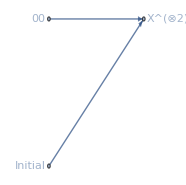

```mathematica
net=QuantumCircuitOperator[{QuantumState["00"],QuantumOperator["X",{1,4}->{1,3}]}]["TensorNetwork",GraphLayout -> {"LayeredDigraphEmbedding", "Orientation" -> Left}]
```

```mathematica
list=Developer`FromPackedArray@VertexList[net];
TableForm[Transpose[Prepend[AnnotationValue[{net,list},#]&/@{"Tensor","Index"},Sort@AnnotationValue[net,VertexLabels]]],]
```

VertexLabel | Tensor | Index
0→Initial | SparseArray[…] | {0^4}
1→00 | SparseArray[…] | {1^1,1^2}
2→X^(⊗2) | SparseArray[…] | {2^1,2^3,2_1,2_4}

```mathematica
EdgeList[net]
```

{12{1^1,2_1},02{0^4,2_4}}

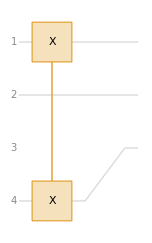

```mathematica
QuantumCircuitOperator[{"X"->{1,4},"Permutation"->{1,4}->{1,3}}]["Diagram"]
```

```mathematica
QuantumCircuitOperator[{"X"->{1,4},"Permutation"->{1,4}->{1,3}}]["CircuitOperator"]==QuantumOperator["X",{1,4}->{1,3}]
```

True

Only output

```mathematica
QuantumOperator[QuantumState["1"]]
```

QuantumOperator[…]

```mathematica
QuantumCircuitOperator[{QuantumOperator[QuantumState["1"]],QuantumOperator@QuantumState[{a,b}]}]
```

QuantumCircuitOperator[…]

```mathematica
QuantumOperator[QuantumState["1"]]["Order"]
```

{{1},{}}

```mathematica
QuantumOperator[QuantumState["1"]]["Tensor"]
```

SparseArray[…]

```mathematica
QuantumOperator[QuantumState[{a,b}]]["Order"]
```

{{1},{}}

```mathematica
?**`Einstein*
```

```mathematica
QuantumState@Flatten@Wolfram`QuantumFramework`PackageScope`EinsteinSummation[{{c[1]},{c[2]}},{QuantumOperator[QuantumState["1"]]["Tensor"],QuantumOperator[QuantumState[{a,b}]]["Tensor"]}]
```

a 10+b 11

```mathematica
QuantumOperator[QuantumState[{a,b,c,d}]]==QuantumOperator[QuantumState[{a,b,c,d}],{1}->{1}]
```

True

```mathematica
QuantumOperator[QuantumState[{a,b,c,d}],{}->{1}]
```

QuantumOperator[…]

```mathematica
QuantumOperator[QuantumState[{a,b,c,d}],{1}->{1}]@QuantumState[{x,y}]
```

QuantumState[…]